```mathematica
｀｀
```

```mathematica
(*
第七讲


一、数列极限的概念

高等数学也称之为微积分，而微积分的中心思想就是极限！

举例：割圆术

-Graphics-

假设圆的半径是1，内嵌正六边形，则图中着色的功能区域面积为：

S = (a6×1)/2 (两条对角线乘积的一半）

从这里可以看到，S是正12边形六分之一的面积，如果仔乘以6的话，也就是正六边形的面积是：3×a6，依此类推：正24边形面积6×a12    
注意：a12>2×a6， 如果内嵌多边形的变数越多，也就意味着面积在逐渐增大 
－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－
圆周率：就是圆周长和半径的比值
－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－
二、数列的定义

按一定规律排列的无穷多个相同或不相同的数
		Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],...,Subscript[a, n] 
也可以简单的记作{Subscript[a, n]}，称之为通项或一般项

-Graphics-

数列的下标都是正整数，因此也被称之为整标函数


数列的表示法：

-Graphics-

-Graphics-

第三种方法叫做散点图：假设通项公式如下：

Subscript[a, n] = (√n)/n (n=1,2,...,10)
*)
```

{1,1/(√2),1/(√3),1/2,1/(√5),1/(√6),1/(√7),1/(2 √2),1/3,1/(√10)}

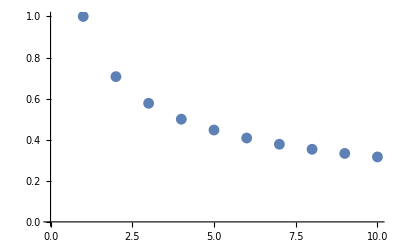

```mathematica
d = Table[(√n)/n,{n,1,10}]
ListPlot[d]
```

```mathematica
(*
－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－

三、数列极限的定义

-Graphics-
极限的几何定义
-Graphics-


－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－－

四、割圆术计算圆周率--祖冲之

** 圆周率 π 有啥用? **

1. 圆的周长是直径的3倍     周长公式：C = 2πr ＝ 直径 × π
2. 圆的面积和半径的平方的比值     面积公式：S = πr^2  
3. 精细的圆周率，可以用来检验计算机的计算正确性
 4. 圆的内切正六边形，它的边长等于圆的半径


看看割圆术中，内切多边形的边的边长是如何计算的？有了边长，想想怎么求它的面积？

-Graphics-
单位圆（也就是半径为1），根据本篇文章开始的割圆术的内容，我们可以知道四边形如何求面积！！！所以内切多边形的面积是：

-Graphics-

其实用割圆术求 π（单位圆面积） 的原理：
就是用假设半径为1，计算不同内切多边形的面积，边数越多，越接近π,也就是π越精细！！！

-Graphics-


题外话：祖冲之爷爷就是用算筹来计算圆周率的，看看算筹的原理，真是没话说～～

-Graphics-       -Graphics-


*)
```